```mathematica
(*Flip-coin measure*)
```

```mathematica
(*Flip-coin measure of a^n b^n: X -> aXb | ϵ *)
∑_(k=0)^∞ (x)^(2k)
Subscript[μ, 1]=FullSimplify @∑_(k=0)^∞ ((1-p)/2)^(2k)p
```

1/(1-x^2)

```mathematica
FullSimplify[(4 p)/(3+2 p-p^2)]
```

(4 p)/(3+2 p-p^2)

```mathematica
Subscript[μ, 1']=FullSimplify @∑_(k=1)^∞ ((1-p)/2)^(2k)p
```

-((-1+p)^2 p)/((-3+p) (1+p))

```mathematica
Subscript[μ, 2]=FullSimplify[∑_(n=0)^∞ ((1-p)/2)^(2n)*p * CatalanNumber[n]]
Reduce @ (Subscript[μ, 2]≥Subscript[μ, 1])
CatalanNumber[1]
```

-(2 p (-1+√(-(-2+p) p)))/(-1+p)^2

0≤p<1||1<p≤2

1

```mathematica
(*Flip-coin measure of L = {w in Σ^*: |w|_a=|w|_b and |u|_a≥|u|_b for every prefix u of w}: Y -> aYbY | ϵ *)
Subscript[μ, 3]=∑_(n=0)^∞ ((1-p)/2)^(2n)*p * Multinomial[2n,n]
Reduce @ (Subscript[μ, 3]≥Subscript[μ, 2])
```

p/(√(-(-2+p) p))

0≤p<1||1<p<2

0≤p<2

-(2 p (-1+√(-(-2+p) p)))/(-1+p)^2

0≤p<1||1<p≤2

```mathematica
(∑_(k=0)^∞ (x^3)^k*Multinomial[k,k,k])
(∑_(k=0)^∞ (x^3)^k*Binomial[3k,k]*Binomial[2k,k])
(∑_(k=0)^∞ (x^3)^k*Factorial[3k]/(Factorial[k])^3)
Binomial[3k,k]*Binomial[2k,k]
```

Hypergeometric2F1[1/3,2/3,1,27 x^3]

Hypergeometric2F1[1/3,2/3,1,27 x^3]

Hypergeometric2F1[1/3,2/3,1,27 x^3]

Binomial[2 k,k] Binomial[3 k,k]

```mathematica
FullSimplify[Binomial[2 k,k] Binomial[3 k,k]]
```

((3 k)!)/(k!)^3

```mathematica
N[1/2 Hypergeometric2F1[1/3,2/3,1,1/8]]
```

0.514946

```mathematica
f[0]:=1
f[n_]:=Sum[Sum[f[m1]*f[m2]*f[n-1-m1-m2],{m2, 0, n-1-m1}],{m1, 0, n-1}]
f/@{0,1,2,3,4,5,6,7,8,9,10}
```

```mathematica
{1,1,3,12,55,273,1428,7752,43263,246675,1430715}
```

{1,1,3,12,55,273,1428,7752,43263,246675,1430715}

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1-μ+μ^k==0]

```mathematica
FullSimplify[μ^4-μ+1]
```

1-μ+μ^4

```mathematica
1-3 x^2+6x
```

1+6 x-3 x^2

```mathematica
FullSimplify[1+6 x-3 x^2]
```

1-3 (-2+x) x

```mathematica
Factor[1-3 (-2+x) x]
```

1+6 x-3 x^2

```mathematica
3-x^2+2x
```

3+2 x-x^2

```mathematica
Factor[3+2 x-x^2]
```

-(-3+x) (1+x)

```mathematica
Sum[x^k*4^k*1/((k+1)(2k+1))Binomial[3k,k],{k,0,Infinity}]
```

(-1+Hypergeometric2F1[-2/3,-1/3,1/2,27 x])/(12 x)

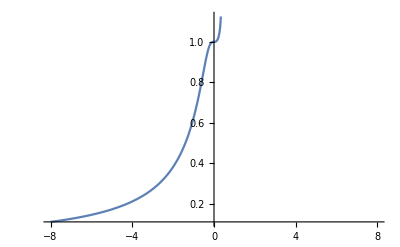

```mathematica
Plot[(-1+Hypergeometric2F1[-2/3,-1/3,1/2,27 x^3])/(12 x^3),{x,-8,8}]
```

```mathematica
TrigReduce[(2 Cos[1/6 ArcCos[1-(27 x^3)/2]])/(√(4-27 x^3))]
```

-(2 √(4-27 x^3) Cos[1/6 ArcCos[1-(27 x^3)/2]])/(-4+27 x^3)

```mathematica
Simplify[-(2 √(4-27 x^3) Cos[1/6 ArcCos[1-(27 x^3)/2]])/(-4+27 x^3)]
```

(2 Cos[1/6 ArcCos[1-(27 x^3)/2]])/(√(4-27 x^3))

```mathematica
Apart[(2 Cos[1/6 ArcCos[1-(27 x^3)/2]])/(√(4-27 x^3)),x]
```

-(2 √(4-27 x^3) Cos[1/6 ArcCos[1-(27 x^3)/2]])/(-4+27 x^3)

```mathematica
TrigToExp[-(2 √(4-27 x^3) Cos[1/6 ArcCos[1-(27 x^3)/2]])/(-4+27 x^3)]
```

-(ⅇ^(-1/6 ⅈ (π/2+ⅈ Log[ⅈ (1-(27 x^3)/2)+√(1-(1-(27 x^3)/2)^2)])) √(4-27 x^3))/(-4+27 x^3)-(ⅇ^(1/6 ⅈ (π/2+ⅈ Log[ⅈ (1-(27 x^3)/2)+√(1-(1-(27 x^3)/2)^2)])) √(4-27 x^3))/(-4+27 x^3)